## PID discretization problem (Problem 5.13)

```mathematica
Clear["Global`*"];
SetOptions[ListPlot,Joined->True,InterpolationOrder->0,PlotRange -> All];
SetOptions[Plot,PlotRange -> All];
```

```mathematica
tmax=5; Ts0=0.1;G0=1/(1+s);K0=1+1/s;  T0=(G0 K0)/(1+G0 K0)//Simplify;
G0tf= TransferFunctionModel[G0,s];K0tf= TransferFunctionModel[K0,s];T0tf= TransferFunctionModel[T0,s];
y0=OutputResponse[T0tf,UnitStep[t],{t,0,tmax}];
py0=Plot[y0,{t,0,tmax},PlotStyle ->{Thick,Red}];
{G0dtf =  ToDiscreteTimeModel[G0tf,Ts0,z,Method -> "ZeroOrderHold"],
K0dtf1=ToDiscreteTimeModel[K0tf,Ts0,z,Method -> "BackwardRectangularRule"],
K0dtf2=ToDiscreteTimeModel[K0tf,Ts0,z,Method -> "BilinearTransform"]}
```

{-0.0951626/(0.904837-1. z)0.1TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`z11-0.095162581964040370.90483741803595961FalseFalseFalseAutomaticNoneAutomatic,(-1+1.1 z)/(-1+z)0.1TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`z11-1-11FalseFalseFalseAutomaticNoneAutomatic,(-1.9+2.1 z)/(2 (-1+z))0.1TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`z11-1.921FalseFalseFalseAutomaticNoneAutomatic}

```mathematica
G0d=Divide@@G0dtf[[1]];  K0d1=Divide@@K0dtf1[[1]]; K0d2=Divide@@K0dtf2[[1]];
T1=Together[(G0d K0d1)/(1+G0d K0d1)];T2=Together[(G0d K0d2)/(1+G0d K0d2)];
{T1tf=TransferFunctionModel[T1,z,SamplingPeriod->Ts0],
T2tf=TransferFunctionModel[T2,z,SamplingPeriod->Ts0]}
```

{(0.104679 (-0.909091+1. z))/(0.809675-1.80016 z+1. z^2)0.1TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`z110.104678840160444420.80967483607191931FalseFalseFalseAutomaticNoneAutomatic,(0.0999207 (-0.904762+1. z))/(0.814433-1.80492 z+1. z^2)0.1TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`z110.09992071106224240.81443296517012131FalseFalseFalseAutomaticNoneAutomatic}

```mathematica
y1=OutputResponse[T1tf,UnitStep[t],{t,0,tmax}][[1]]  (* Backward Euler *);     
y2=OutputResponse[T2tf,UnitStep[t],{t,0,tmax}][[1]]  (* Tustin *);     

py12=ListPlot[{y1,y2},DataRange->{0,5}];
```

So all is good with PI controller .  Now let' s add a bit of D

```mathematica
K0a=1+1/s+0.1s; K0atf= TransferFunctionModel[K0a,s];
K0adtf1=ToDiscreteTimeModel[K0atf,Ts0,z,Method -> "BackwardRectangularRule"];
K0adtf2=ToDiscreteTimeModel[K0atf,Ts0,z,Method -> "BilinearTransform"];
 K0ad1=Divide@@K0adtf1[[1]]; K0ad2=Divide@@K0adtf2[[1]];
T1a=Together[(G0d K0ad1)/(1+G0d K0ad1)];T2a=Together[(G0d K0ad2)/(1+G0d K0ad2)];

T1atf=TransferFunctionModel[T1a,z,SamplingPeriod->Ts0];
T2atf=TransferFunctionModel[T2a,z,SamplingPeriod->Ts0];

y1a=OutputResponse[T1atf,UnitStep[t],{t,0,tmax}][[1]]  (* Backward Euler *);     
y2a=OutputResponse[T2atf,UnitStep[t],{t,0,tmax}][[1]]  (* Tustin *);     

py12a=ListPlot[{y1a,y2a},DataRange->{0,5}];
py2a=ListPlot[y2a,DataRange->{0,5},PlotStyle ->{Blue},PlotRange -> {-1,2}];
{K0ad1,K0ad2}  (* note pole at z=-1 for K0ad2 *)
```

{{{(2.1 (0.47619-1.42857 z+1. z^2))/((-1+z) z)}},{{(3.05 (0.344262-1.27869 z+1. z^2))/((-1+z) (1.+z))}}}

```mathematica
{T1atf,T2atf}
```

{(0.199841 (0.47619-1.42857 z+1. z^2))/(0.0951626+0.61935 z-1.705 z^2+1. z^3)0.1TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`z110.19984142212448480.095162581964040371FalseFalseFalseAutomaticNoneAutomatic,(0.290246 (0.344262-1.27869 z+1. z^2))/(1.00476-1.37113 z-0.614592 z^2+1. z^3)0.1TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`z110.29024587499032321.0047581290982021FalseFalseFalseAutomaticNoneAutomatic}

```mathematica
poles1=TransferFunctionPoles[T1atf]
```

{{{-0.114874,0.909935-0.0205924 ⅈ,0.909935+0.0205924 ⅈ}}}

```mathematica
Abs[poles1] (* all stable *)
```

{{{0.114874,0.910168,0.910168}}}

```mathematica
poles2=TransferFunctionPoles[T2atf]
```

{{{-1.20832,0.911457-0.0279038 ⅈ,0.911457+0.0279038 ⅈ}}}

```mathematica
Abs[poles2] (* uh oh.... *)
```

{{{1.20832,0.911884,0.911884}}}

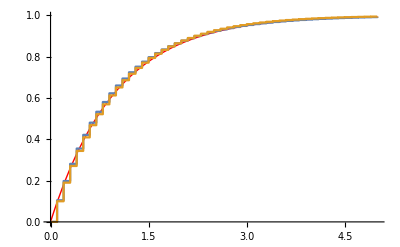
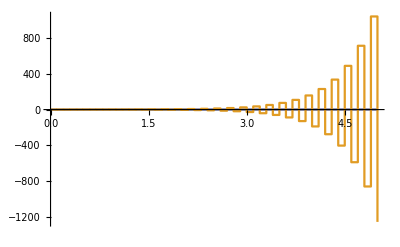

```mathematica
{Show[py0,py12],Show[py0,py12a]}
```

Export data

```mathematica
(* SetDirectory[NotebookDirectory[]] *)
```

```mathematica
dat=Table[{y0[[1]]},{t,0,tmax,Ts0/10}];  (* continuous system *)
(* 
SetDirectory[NotebookDirectory[]];Export["PIDdiscretization.dat", dat]; 
Export["PIDdiscretization.dat", {y1,y2,y1a,y2a}ᵀ];  (* discrete sys *)
*)
```

Table of transfer functions illustrating different discretization algorithms

```mathematica
tfm=1/sTransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s11$CellContext`s11FalseFalseFalseAutomaticNoneAutomatic;
Grid[tfmd=Table[{m,ToDiscreteTimeModel[tfm,Ts,z,Method->m]},{m,{"ForwardRectangularRule","BackwardRectangularRule","BilinearTransform","ZeroOrderHold","FirstOrderHold"}}],Background->{None,{{White,LightGray}}},Frame->All]
```

ForwardRectangularRule | Ts/(-1+z)TsTransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`z111$CellContext`Ts1FalseFalseFalseAutomaticNoneAutomatic
BackwardRectangularRule | (Ts z)/(-1+z)TsTransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`z11$CellContext`Ts-11FalseFalseFalseAutomaticNoneAutomatic
BilinearTransform | (Ts (1+z))/(2 (-1+z))TsTransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`z11$CellContext`Ts21FalseFalseFalseAutomaticNoneAutomatic
ZeroOrderHold | -Ts/(1-z)TsTransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`z11$CellContext`Ts11FalseFalseFalseAutomaticNoneAutomatic
FirstOrderHold | (-Ts/2-(Ts z)/2)/(1-z)TsTransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`z11-111FalseFalseFalseAutomaticNoneAutomatic